```mathematica
datapath ="C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Same inputs\\All_Data\\";
datapathAB ="C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Same inputs\\Corrected_A_and_B_Capacitance\\";
datapathExchanged = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Inductance_exchange\\All Data\\";
(* 
Tol: Increased tolerances by about factor 3 or 5
Rser: Increased serial resistance by about factor 3 or 5
Rand Rser: Random fluctuation of serial resistance (Gaussian)
 *)
importdata = Import[#,"Table"]&/@(FileNames[datapath<>"eti_single_layer_hermitian_*.txt"]);
importdataAB = Import[#,"Table"]&/@(FileNames[datapathAB<>"eti_single_layer_hermitian_*.txt"]);
importdataExchanged = Import[#,"Table"]&/@(FileNames[datapathExchanged<>"eti_single_layer_hermitian_*.txt"]);
importdata//Dimensions
```

{28,1001,3}

```mathematica
importdata[[2,2;;10,1]]//MatrixForm
```

(100000.
109910.
119820.
129730.
139640.
149550.
159459.
169369.
179279.)

```mathematica
convertedData=Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importdata[[node,i,j]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{node,1,Dimensions[importdata][[1]]},{i,2,Dimensions[importdata][[2]]},{j,2,Dimensions[importdata][[3]]}];

impedanceData = Table[(convertedData[[node,i,1]])/(convertedData[[node,i,-1]]),{node,1,Dimensions[convertedData][[1]]},{i,2,Dimensions[convertedData][[2]]}];

freqData = Table[Block[{expr = ToExpression[importdata[[node,i,1]]]},expr],{node,1,Dimensions[importdata][[1]]},{i,2,Dimensions[importdata][[2]]}];
```

```mathematica
convertedDataAB=Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importdataAB[[node,i,j]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{node,1,Dimensions[importdataAB][[1]]},{i,2,Dimensions[importdataAB][[2]]},{j,2,Dimensions[importdataAB][[3]]}];

impedanceDataAB = Table[(convertedDataAB[[node,i,1]])/(convertedDataAB[[node,i,-1]]),{node,1,Dimensions[convertedDataAB][[1]]},{i,2,Dimensions[convertedDataAB][[2]]}];

freqDataAB = Table[Block[{expr = ToExpression[importdataAB[[node,i,1]]]},expr],{node,1,Dimensions[importdataAB][[1]]},{i,2,Dimensions[importdataAB][[2]]}];
```

```mathematica
convertedDataExchanged=Table[Block[{reIm = ToExpression[StringReplace[StringSplit[importdataExchanged[[node,i,j]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{node,1,Dimensions[importdataExchanged][[1]]},{i,2,Dimensions[importdataExchanged][[2]]},{j,2,Dimensions[importdataExchanged][[3]]}];

impedanceDataExchanged = Table[(convertedDataExchanged[[node,i,1]])/(convertedDataExchanged[[node,i,-1]]),{node,1,Dimensions[convertedDataExchanged][[1]]},{i,2,Dimensions[convertedDataExchanged][[2]]}];

freqDataExchanged = Table[Block[{expr = ToExpression[importdataExchanged[[node,i,1]]]},expr],{node,1,Dimensions[importdataExchanged][[1]]},{i,2,Dimensions[importdataExchanged][[2]]}];
```

```mathematica
shift = 0;
ticks = Table[{(Dimensions[freqData][[2]])/10*i,ToString[i]},{i,1,10}];
tickShift = Table[ticks[[i]]-{shift,0},{i,1,10}];
```

```mathematica
impedanceDataAbs = Table[{importdata[[2,i+1,1]],Abs[impedanceData[[node,i]]]},{node,1,Dimensions[impedanceData][[1]]},{i,shift+1,Dimensions[impedanceData][[2]]}];
```

```mathematica
impedanceDataAbsAB = Table[{importdataAB[[2,i+1,1]],Abs[impedanceDataAB[[node,i]]]},{node,1,Dimensions[impedanceDataAB][[1]]},{i,shift+1,Dimensions[impedanceDataAB][[2]]}];
```

```mathematica
impedanceDataPhase = Table[{importdata[[2,i+1,1]],Arg[impedanceData[[node,i]]]},{node,1,Dimensions[impedanceData][[1]]},{i,shift+1,Dimensions[impedanceData][[2]]}];
```

```mathematica
impedanceDataPhaseAB = Table[{importdataAB[[2,i+1,1]],Arg[impedanceDataAB[[node,i]]]},{node,1,Dimensions[impedanceDataAB][[1]]},{i,shift+1,Dimensions[impedanceDataAB][[2]]}];
```

```mathematica
impedanceDataAbsExchanged = Table[{importdataExchanged[[2,i+1,1]],Abs[impedanceDataExchanged[[node,i]]]},{node,1,Dimensions[impedanceDataExchanged][[1]]},{i,shift+1,Dimensions[impedanceDataExchanged][[2]]}];
```

```mathematica
impedanceDataPhaseExchanged = Table[{importdataExchanged[[2,i+1,1]],Arg[impedanceDataExchanged[[node,i]]]},{node,1,Dimensions[impedanceDataExchanged][[1]]},{i,shift+1,Dimensions[impedanceDataExchanged][[2]]}];
```

```mathematica
impedancePlotsAbs = Table[ListLinePlot[Abs[impedanceData[[node,(shift+1);;]]],PlotRange->All,PlotLabel->"Config "<>ToString[Floor[node+1,2]/2]<>": "<>ToString[importdata[[node,1,2]]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy [MHz]","Amplitude"}],{node,1,Dimensions[impedanceData][[1]]}];
```

```mathematica
impedancePlotsAbsAB = Table[ListLinePlot[Abs[impedanceDataAB[[node,(shift+1);;]]],PlotRange->All,PlotLabel->"Config "<>ToString[Floor[node+1,2]/2]<>": "<>ToString[importdataAB[[node,1,2]]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy [MHz]","Amplitude"}],{node,1,Dimensions[impedanceDataAB][[1]]}];
```

```mathematica
impedancePlotsAbsExchanged = Table[ListLinePlot[Abs[impedanceDataExchanged[[node,(shift+1);;]]],PlotRange->All,PlotLabel->"Config "<>ToString[Floor[node+1,2]/2]<>": "<>ToString[importdataExchanged[[node,1,2]]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy [MHz]","Amplitude"}],{node,1,Dimensions[impedanceDataExchanged][[1]]}];
```

```mathematica
impedancePlotsPhase = Table[ListLinePlot[Arg[impedanceData[[node,(shift+1);;]]],PlotRange->All,PlotLabel->"Config "<>ToString[Floor[node+1,2]/2]<>": "<>ToString[importdata[[node,1,2]]],Ticks->{tickShift,Automatic},AxesLabel->{"Frequenzy [MHz]","Phase"}],{node,1,Dimensions[impedanceData][[1]]}];
```

```mathematica
Manipulate[impedancePlotsAbs[[node]],{node,1,Dimensions[impedanceData][[1]],1}]
```

Part::partd: Part specification impedancePlotsAbs⟦1⟧ is longer than depth of object.

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];
```

```mathematica
pathETIWithinGit="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\";
pathWithMult=pathETIWithinGit<>"Data\\singling_out_device_parts\\obc_single_layer_2022_09_13\\Layer_01\\";
pathWithMultSandwich=pathETIWithinGit<>"Data\\singling_out_device_parts\\ETI Single Layer tests\\2022_09_04\\board_08\\";
pathByHand=pathETIWithinGit<>"Data\\singling_out_device_parts\\comparison_multiplexer_no_multiplexer\\byHand\\";
```

```mathematica
impWithMult=Import[#,"Table",HeaderLines->2]&/@(FileNames[pathWithMult<>"2D_*.dat"]);
impWithMultSandwich=Import[#,"Table",HeaderLines->2]&/@(FileNames[pathWithMultSandwich<>"2D_*.dat"]);
impByHand=Import[#,"Table",HeaderLines->2]&/@(FileNames[pathByHand<>"2D_*.dat"]);
```

```mathematica
impWithMult[[1,1]]
```

{100000.,1604.78,-45.1907,1130.82,-0.00181181}

```mathematica
sortedDataWithMult//Dimensions
sortedDataWithMult[[1,1,2,1]]
sortedDataWithMult[[1;;All;;2,All,2,1,{1,2}]]//Dimensions
sortedDataWithMult[[1;;All;;2,All,2,1,{1,3}]]
```

{8,4,2}

{100000.,1623.46,-45.6327,1135.08,-0.00184651}

{4,4,2}

{{{100000.,-45.6327},{100000.,-45.5437},{100000.,-45.7643},{100000.,-45.1909}},{{100000.,-45.6057},{100000.,-45.4253},{100000.,-44.7556},{100000.,-45.4807}},{{100000.,-45.4333},{100000.,-45.3342},{100000.,-46.4988},{100000.,-45.2593}},{{100000.,-45.4894},{100000.,-45.6627},{100000.,-44.9321},{100000.,-45.5518}}}

```mathematica
nodeCoordAndDataWithMult=Transpose[{p1,impWithMult}];
sortedDataWithMult=Partition[SortBy[nodeCoordAndDataWithMult,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];

nodeCoordAndDataWithMultSandwich=Transpose[{p1,impWithMultSandwich[[;;32]]}];
sortedDataWithMultSandwich=Partition[SortBy[nodeCoordAndDataWithMultSandwich,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];
```

```mathematica
nodeCoordAndDataByHand=Transpose[{p1,impByHand}];
sortedDataByHand=Partition[SortBy[nodeCoordAndDataByHand,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];
```

```mathematica
subAExpWithMultplexerPlotReady=sortedDataWithMult[[1;;All;;2,All,2,All,{1,2}]];
subBExpWithMultplexerPlotReady=sortedDataWithMult[[2;;All;;2,All,2,All,{1,2}]];

subAExpWithMultplexerPlotReadySandwich=sortedDataWithMultSandwich[[1;;All;;2,All,2,All,{1,2}]];
subBExpWithMultplexerPlotReadySandwich=sortedDataWithMultSandwich[[2;;All;;2,All,2,All,{1,2}]];
```

```mathematica
subMan = {subAExpWithMultplexerPlotReady,subBExpWithMultplexerPlotReady};
Manipulate[ListLinePlot[subMan[[sub,x,y]],PlotRange->All,ImageSize->Large],{sub,1,2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification subMan⟦1,3,1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: subMan⟦1,3,1⟧ is not a list of numbers or pairs of numbers.

```mathematica
subAExpWithMultplexerPhasePlotReady=sortedDataWithMult[[1;;All;;2,All,2,All,{1,3}]];
subBExpWithMultplexerPhasePlotReady=sortedDataWithMult[[2;;All;;2,All,2,All,{1,3}]];

subAExpWithMultplexerPhasePlotReadySandwich=sortedDataWithMultSandwich[[1;;All;;2,All,2,All,{1,3}]];
subBExpWithMultplexerPhasePlotReadySandwich=sortedDataWithMultSandwich[[2;;All;;2,All,2,All,{1,3}]];
```

```mathematica
subAByHandExpPlotReady=sortedDataByHand[[1;;All;;2,All,2,All,{1,2}]];
subBByHandExpPlotReady=sortedDataByHand[[2;;All;;2,All,2,All,{1,2}]];
```

```mathematica
subAByHandExpPhasePlotReady=sortedDataByHand[[1;;All;;2,All,2,All,{1,3}]];
subBByHandExpPhasePlotReady=sortedDataByHand[[2;;All;;2,All,2,All,{1,3}]];
```

```mathematica
subAByHandExpPlotReady//Dimensions
```

{4,4,513,2}

```mathematica
subMan = {subAByHandExpPlotReady,subBByHandExpPlotReady};
Manipulate[ListPlot[subMan[[sub,x,y]],PlotRange->All,ImageSize->Large],{sub,1,2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification subMan⟦1,1,1⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: subMan⟦1,1,1⟧ is not a list of numbers or pairs of numbers.

```mathematica
subASpan=1;;All;;2;
subBSpan=2;;All;;2;
```

```mathematica
MultiplexerAverageSubA = Table[Mean[Flatten[subAExpWithMultplexerPlotReady[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPlotReady[[1,1,;;,2]]]}];

MultiplexerAverageSTDSubA = Table[Around[Mean[Flatten[subAExpWithMultplexerPlotReady[[;;,;;,i,2]]]],StandardDeviation[Flatten[subAExpWithMultplexerPlotReady[[;;,;;,i,2]]]]],{i,1,Length[subAExpWithMultplexerPlotReady[[1,1,;;,2]]]}];

MultiplexerAverageSubASandwich = Table[Mean[Flatten[subAExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPlotReadySandwich[[1,1,;;,2]]]}];

MultiplexerAverageSTDSubASandwich = Table[Around[Mean[Flatten[subAExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]],StandardDeviation[Flatten[subAExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]]],{i,1,Length[subAExpWithMultplexerPlotReadySandwich[[1,1,;;,2]]]}];
```

```mathematica
MultiplexerAveragePhaseSubA = Table[Mean[Flatten[subAExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPhasePlotReady[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSTDSubA = Table[Around[Mean[Flatten[subAExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]],StandardDeviation[Flatten[subAExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]]],{i,1,Length[subAExpWithMultplexerPhasePlotReady[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSubASandwich = Table[Mean[Flatten[subAExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPhasePlotReadySandwich[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSTDSubASandwich = Table[Around[Mean[Flatten[subAExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]],StandardDeviation[Flatten[subAExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]]],{i,1,Length[subAExpWithMultplexerPhasePlotReadySandwich[[1,1,;;,2]]]}];
```

Part::partd: Part specification subAExpWithMultplexerPhasePlotReady⟦1,1,1;;All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification subAExpWithMultplexerPhasePlotReady⟦1,1,1;;All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification subAExpWithMultplexerPhasePlotReadySandwich⟦1,1,1;;All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partd: Part specification subAExpWithMultplexerPhasePlotReadySandwich⟦1,1,1;;All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
MultiplexerAverageSubB = Table[Mean[Flatten[subBExpWithMultplexerPlotReady[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPlotReady[[1,1,;;,2]]]}];

MultiplexerAverageSTDSubB = Table[Around[Mean[Flatten[subBExpWithMultplexerPlotReady[[;;,;;,i,2]]]],StandardDeviation[Flatten[subBExpWithMultplexerPlotReady[[;;,;;,i,2]]]]],{i,1,Length[subBExpWithMultplexerPlotReady[[1,1,;;,2]]]}];

MultiplexerAverageSubBSandwich = Table[Mean[Flatten[subBExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]],{i,1,Length[subAExpWithMultplexerPlotReadySandwich[[1,1,;;,2]]]}];

MultiplexerAverageSTDSubBSandwich = Table[Around[Mean[Flatten[subBExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]],StandardDeviation[Flatten[subBExpWithMultplexerPlotReadySandwich[[;;,;;,i,2]]]]],{i,1,Length[subBExpWithMultplexerPlotReadySandwich[[1,1,;;,2]]]}];
```

```mathematica
MultiplexerAveragePhaseSubB = Table[Mean[Flatten[subBExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]],{i,1,Length[subBExpWithMultplexerPhasePlotReady[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSTDSubB = Table[Around[Mean[Flatten[subBExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]],StandardDeviation[Flatten[subBExpWithMultplexerPhasePlotReady[[;;,;;,i,2]]]]],{i,1,Length[subBExpWithMultplexerPhasePlotReady[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSubBSandwich = Table[Mean[Flatten[subBExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]],{i,1,Length[subBExpWithMultplexerPhasePlotReadySandwich[[1,1,;;,2]]]}];

MultiplexerAveragePhaseSTDSubBSandwich = Table[Around[Mean[Flatten[subBExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]],StandardDeviation[Flatten[subBExpWithMultplexerPhasePlotReadySandwich[[;;,;;,i,2]]]]],{i,1,Length[subBExpWithMultplexerPhasePlotReadySandwich[[1,1,;;,2]]]}];
```

```mathematica
2π/(10^6)//N
```

6.28319×10^-6

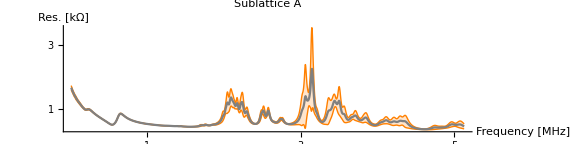
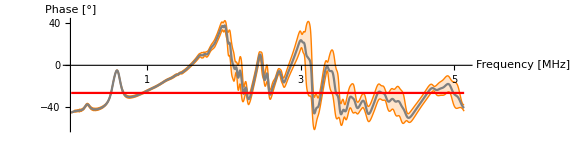

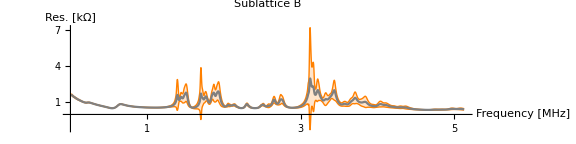
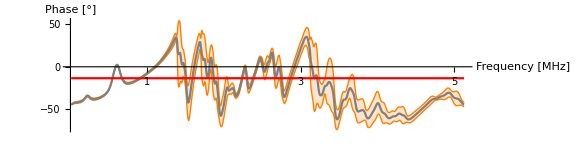

```mathematica
meanPhaseSubA = Mean[MultiplexerAveragePhaseSubA[[;;150]]];
meanPhaseLineSubA = Table[meanPhaseSubA,{i,1,Length[MultiplexerAverageSTDSubA]}];
Grid[{{ListLinePlot[MultiplexerAverageSTDSubA,PlotLabel->"Sublattice A",IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Amplitudes over all A Nodes with Multiplexer"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]},{ListLinePlot[{MultiplexerAveragePhaseSTDSubA,meanPhaseLineSubA},IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Phases over all A Nodes with Multiplexer","Average Phase over whole Spectrum with Multiplexer"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,Automatic},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Phase [°]"}]}}]

meanPhaseSubB = Mean[MultiplexerAveragePhaseSubB[[;;150]]];
meanPhaseLineSubB = Table[meanPhaseSubB,{i,1,Length[MultiplexerAverageSTDSubB]}];
Grid[{{ListLinePlot[MultiplexerAverageSTDSubB,PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Amplitudes over all B Nodes with Multiplexer"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]},{ListLinePlot[{MultiplexerAveragePhaseSTDSubB,meanPhaseLineSubB},IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Phases over all B Nodes with Multiplexer","Average Phase over whole Spectrum with Multiplexer"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,Automatic},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Phase [°]"}]}}]
```

```mathematica
config = 7;
ListLinePlot[{MultiplexerAverageSTDSubA,impedanceDataAbs[[(config-1)*2+1,;;513,2]]},PlotLabel->"Sublattice A",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement","Simulation"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]

	
ListLinePlot[{MultiplexerAverageSTDSubB,impedanceDataAbs[[(config-1)*2+2,;;513,2]]},PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement","Simulation"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]
```

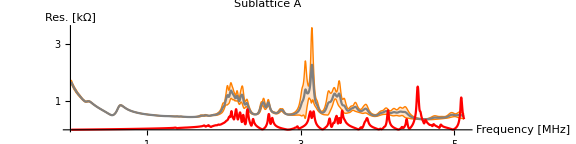

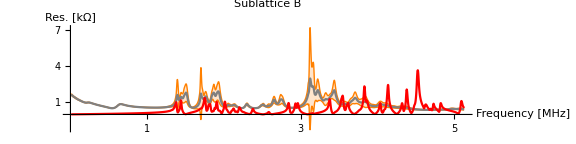

```mathematica
configEx = 6;
percentage = 50;
ListLinePlot[{MultiplexerAverageSTDSubA,impedanceDataAbsExchanged[[(configEx-1)*2+1,;;513,2]]},PlotLabel->"Sublattice A",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement","Simulation "<>ToString[percentage]<>"% of L = 270μH"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]

	
ListLinePlot[{MultiplexerAverageSTDSubB,impedanceDataAbsExchanged[[(configEx-1)*2+2,;;513,2]]},PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement","Simulation "<>ToString[percentage]<>"% of L = 270μH"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]
```

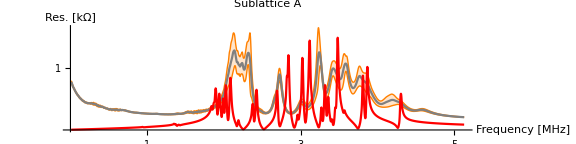
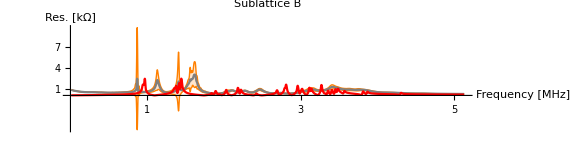

```mathematica
configAB = 3;
ListLinePlot[{MultiplexerAverageSTDSubASandwich,impedanceDataAbsAB[[(configAB-1)*2+1,;;513,2]]},PlotLabel->"Sublattice A",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement Sandwich","Simulation Sandwich"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]

	
ListLinePlot[{MultiplexerAverageSTDSubBSandwich,impedanceDataAbsAB[[(configAB-1)*2+2,;;513,2]]},PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Measurement Sandwich","Simulation Sandwich"},InterpolationOrder->3,AspectRatio->1/4,Ticks->{tickShift,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},ImageSize->Large,AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}]
```

```mathematica
MultiplexerAverageSTDSubB//Dimensions
impedanceDataAbs[[(config-1)*2+2,200,2]]
```

{513}

631.108

```mathematica
comparisonPlotSubA = Table[Show[ListLinePlot[subAExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",A}"],
ListLinePlot[subAByHandExpPlotReady[[x,y]],PlotStyle->Green],
ListLinePlot[impedanceDataAbs[[(node-1)*2+1]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceData][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
comparisonPlotSubB = Table[Show[ListLinePlot[subBExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",B}"],ListLinePlot[impedanceDataAbs[[(node-1)*2+2]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceData][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
Manipulate[comparisonPlotSubA[[node,x,y]],{node,1,(Dimensions[impedanceData][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubA⟦1,3,1⟧ is longer than depth of object.

```mathematica
Manipulate[comparisonPlotSubB[[node,x,y]],{node,1,(Dimensions[impedanceData][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubB⟦1,3,1⟧ is longer than depth of object.

```mathematica
comparisonPlotSubAExchanged = Table[Show[ListLinePlot[subAExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",A}"],
ListLinePlot[impedanceDataAbsExchanged[[(node-1)*2+1]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceDataExchanged][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
comparisonPlotSubBExchanged = Table[Show[ListLinePlot[subBExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",B}"],ListLinePlot[impedanceDataAbsExchanged[[(node-1)*2+2]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceDataExchanged][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
Manipulate[comparisonPlotSubAExchanged[[node,x,y]],{node,1,(Dimensions[impedanceDataExchanged][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubAExchanged⟦1,1,1⟧ is longer than depth of object.

```mathematica
Manipulate[comparisonPlotSubBExchanged[[node,x,y]],{node,1,(Dimensions[impedanceDataExchanged][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubBExchanged⟦1,1,1⟧ is longer than depth of object.

```mathematica
comparisonPlotSubASandwichAB = Table[Show[ListLinePlot[subAExpWithMultplexerPlotReadySandwich[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer AB"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",A}"],
ListLinePlot[impedanceDataAbsAB[[(node-1)*2+1]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceDataAB][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
comparisonPlotSubBSandwichAB = Table[Show[ListLinePlot[subBExpWithMultplexerPlotReadySandwich[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement with Multiplexer AB"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",B}"],ListLinePlot[impedanceDataAbsAB[[(node-1)*2+2]],PlotRange->All,PlotRange->Blue,PlotLegends->{"Theory: "<>"Config "<>ToString[node]}]],{node,1,(Dimensions[impedanceDataAB][[1]])/2},{x,1,4},{y,1,4}];
```

```mathematica
Manipulate[comparisonPlotSubASandwichAB[[node,x,y]],{node,1,(Dimensions[impedanceDataAB][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubASandwichAB⟦1,1,1⟧ is longer than depth of object.

```mathematica
Manipulate[comparisonPlotSubBSandwichAB[[node,x,y]],{node,1,(Dimensions[impedanceDataAB][[1]])/2,1},{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubBSandwichAB⟦1,1,1⟧ is longer than depth of object.

```mathematica
comparisonPlotSubASandwich = Table[Show[ListLinePlot[subAExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement Single Layer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",A}"],
ListLinePlot[subAExpWithMultplexerPlotReadySandwich[[x,y]],PlotRange->All,PlotStyle->Blue,PlotLegends->{"Measurement Sandwich"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",A}"]],{x,1,4},{y,1,4}];
```

```mathematica
comparisonPlotSubBSandwich = Table[Show[ListLinePlot[subBExpWithMultplexerPlotReady[[x,y]],PlotRange->All,PlotStyle->Orange,PlotLegends->{"Measurement Single Layer"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",B}"],
ListLinePlot[subBExpWithMultplexerPlotReadySandwich[[x,y]],PlotRange->All,PlotStyle->Blue,PlotLegends->{"Measurement Sandwich"},PlotLabel->"{"ToString[x]<>","<>ToString[y]<>",B}"]],{x,1,4},{y,1,4}];
```

```mathematica
Manipulate[comparisonPlotSubASandwich[[x,y]],{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubASandwich⟦1,1⟧ is longer than depth of object.

```mathematica
Manipulate[comparisonPlotSubBSandwich[[x,y]],{x,1,4,1},{y,1,4,1}]
```

Part::partd: Part specification comparisonPlotSubBSandwich⟦1,1⟧ is longer than depth of object.

```mathematica
treshA = 0.40;
treshB = 0.40;
maxDetectA =MaxDetect[MultiplexerAverageSubA,Max[MultiplexerAverageSubA]*treshA];
maxDetectB =MaxDetect[MultiplexerAverageSubB,Max[MultiplexerAverageSubB]*treshB];
lowerFreqBound = Ceiling[(0.5*10^6)/(subAExpWithMultplexerPlotReady[[1,1,2,1]]-subAExpWithMultplexerPlotReady[[1,1,1,1]])];
posDiff = Length[maxDetectA]-Length[maxDetectA[[lowerFreqBound;;]]];
subAPoints = Flatten[Position[maxDetectA[[lowerFreqBound;;]],1]+posDiff];
subBPoints=Flatten[Position[maxDetectB[[lowerFreqBound;;]],1]+posDiff];
```

```mathematica
squareDevTheoryExp =Table[Block[{fA=Interpolation[impedanceDataAbs[[node*2-1,;;Length[MultiplexerAverageSubA]]],InterpolationOrder->3],fB=Interpolation[impedanceDataAbs[[node*2,;;Length[MultiplexerAverageSubB]]],InterpolationOrder->3],maxDetectA =MaxDetect[MultiplexerAverageSubA,Max[MultiplexerAverageSubA]*treshA],maxDetectB =MaxDetect[MultiplexerAverageSubB,Max[MultiplexerAverageSubB]*treshB],freqs = subAExpWithMultplexerPlotReady[[1,1,;;,1]],freqDiff = subAExpWithMultplexerPlotReady[[1,1,2,1]]-subAExpWithMultplexerPlotReady[[1,1,1,1]]},{Sum[Abs[fA[10^5+i*freqDiff]-(MultiplexerAverageSubA[[i]])],{i,subAPoints}]/Length[freqs],Sum[Abs[fB[10^5+i*freqDiff]-(MultiplexerAverageSubB[[i]])],{i,subBPoints}]/Length[freqs]}],{node,1,(Dimensions[impedanceDataAbs][[1]])/2}];
idealNodeA = Position[squareDevTheoryExp[[;;,1]],Min[squareDevTheoryExp[[;;,1]]]][[1,1]];
idealNodeB = Position[squareDevTheoryExp[[;;,2]],Min[squareDevTheoryExp[[;;,2]]]][[1,1]];
```

```mathematica
MSEPlotA =Show[ListLinePlot[MultiplexerAverageSTDSubA,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average of Measurements with Multiplexer"},InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[idealNodeA*2-1,;;Length[subAExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],PlotRange->All,Ticks->{tickShift,Automatic},PlotStyle->Red,PlotLegends->{"Theory: "<>"Config "<>ToString[idealNodeA]}]];

MSEPlotB=Show[ListLinePlot[MultiplexerAverageSTDSubB,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average of Measurements with Multiplexer"},InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[idealNodeB*2,;;Length[subBExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],PlotRange->All,Ticks->{tickShift,Automatic},PlotStyle->Red,PlotLegends->{"Theory: "<>"Config "<>ToString[idealNodeB]}]];
```

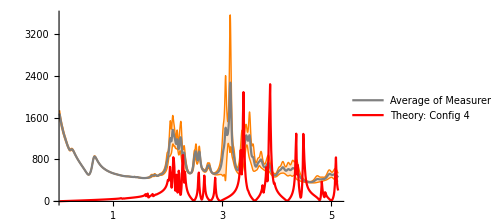
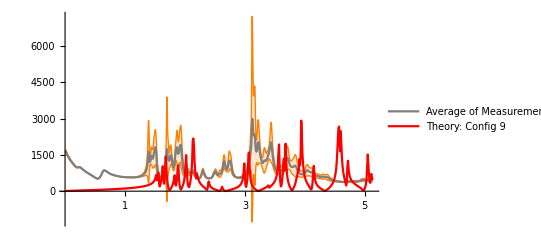
-Graphics- | -Graphics-
 |

```mathematica
Grid[{{MSEPlotA,MSEPlotB},{}}]
```

```mathematica
squareDevTheoryExpExchanged =Table[Block[{fA=Interpolation[impedanceDataAbsExchanged[[node*2-1,;;Length[MultiplexerAverageSubA]]],InterpolationOrder->3],fB=Interpolation[impedanceDataAbsExchanged[[node*2,;;Length[MultiplexerAverageSubB]]],InterpolationOrder->3],maxDetectA =MaxDetect[MultiplexerAverageSubA,Max[MultiplexerAverageSubA]*treshA],maxDetectB =MaxDetect[MultiplexerAverageSubB,Max[MultiplexerAverageSubB]*treshB],freqs = subAExpWithMultplexerPlotReady[[1,1,;;,1]],freqDiff = subAExpWithMultplexerPlotReady[[1,1,2,1]]-subAExpWithMultplexerPlotReady[[1,1,1,1]]},{Sum[Abs[fA[10^5+i*freqDiff]-(MultiplexerAverageSubA[[i]])],{i,subAPoints}]/Length[freqs],Sum[Abs[fB[10^5+i*freqDiff]-(MultiplexerAverageSubB[[i]])],{i,subBPoints}]/Length[freqs]}],{node,1,(Dimensions[impedanceDataAbsExchanged][[1]])/2}];
idealNodeAExchanged = Position[squareDevTheoryExpExchanged[[;;,1]],Min[squareDevTheoryExpExchanged[[;;,1]]]][[1,1]];
idealNodeBExchanged = Position[squareDevTheoryExpExchanged[[;;,2]],Min[squareDevTheoryExpExchanged[[;;,2]]]][[1,1]];
```

```mathematica
MSEPlotAExchanged =Show[ListLinePlot[MultiplexerAverageSTDSubA,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average of Measurements with Multiplexer"},InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbsExchanged[[4*2-1,;;Length[subAExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red,PlotLegends->{"Theory: "<>"Config "<>ToString[idealNodeAExchanged]}]];

MSEPlotBExchanged=Show[ListLinePlot[MultiplexerAverageSTDSubB,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average of Measurements with Multiplexer"},InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbsExchanged[[4*2,;;Length[subBExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red,PlotLegends->{"Theory: "<>"Config "<>ToString[idealNodeBExchanged]}]];
```

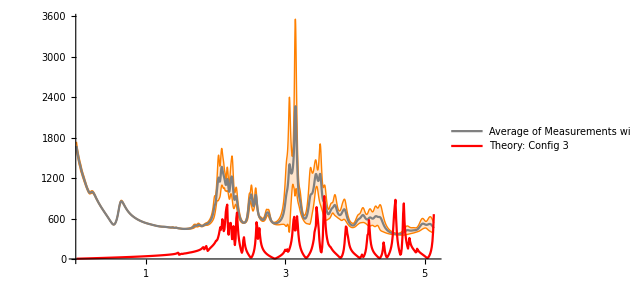
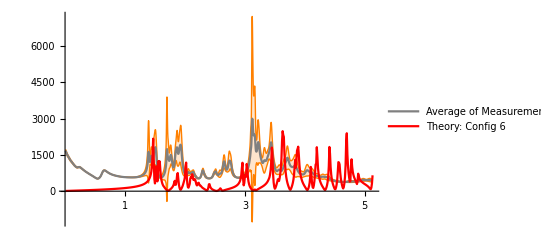
-Graphics- | -Graphics-
 |

```mathematica
Grid[{{MSEPlotAExchanged,MSEPlotBExchanged},{}}]
```

```mathematica
MSEPlotAByHand =
Table[Show[ListLinePlot[MultiplexerAverageSTDSubA,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[node*2-1,;;Length[subAExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red]],{node,1,(Dimensions[impedanceDataAbs][[1]])/2}];

MSEPlotBByHand=
Table[Show[ListLinePlot[MultiplexerAverageSTDSubB,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[node*2,;;Length[subBExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red]],{node,1,(Dimensions[impedanceDataAbs][[1]])/2}];
```

```mathematica
Manipulate[Grid[{{MSEPlotAByHand[[node]],MSEPlotBByHand[[node]]},{}}],{node,1,(Dimensions[impedanceDataAbsExchanged][[1]])/2,1},ControlType->VerticalSlider]
```

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBByHand⟦1⟧ is longer than depth of object.

```mathematica
MSEPlotAExchangedByHand =Table[Show[ListLinePlot[MultiplexerAverageSTDSubA,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[node*2-1,;;Length[subAExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red]],{node,1,(Dimensions[impedanceDataAbsExchanged][[1]])/2}];

MSEPlotBExchangedByHand=Table[Show[ListLinePlot[MultiplexerAverageSTDSubB,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,InterpolationOrder->3,Ticks->{tickShift,Automatic}],ListLinePlot[impedanceDataAbs[[node*2,;;Length[subBExpWithMultplexerPlotReady[[1,1,;;,1]]],2]],Ticks->{tickShift,Automatic},PlotRange->All,PlotStyle->Red]],{node,1,(Dimensions[impedanceDataAbsExchanged][[1]])/2}];
```

```mathematica
Manipulate[Grid[{{MSEPlotAExchangedByHand[[node]],MSEPlotBExchangedByHand[[node]]},{}}],{node,1,(Dimensions[impedanceDataAbsExchanged][[1]])/2,1}]
```

Part::partd: Part specification MSEPlotAExchangedByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBExchangedByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAExchangedByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBExchangedByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotAExchangedByHand⟦1⟧ is longer than depth of object.

Part::partd: Part specification MSEPlotBExchangedByHand⟦1⟧ is longer than depth of object.

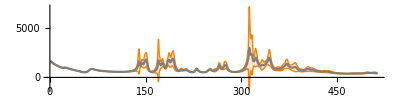

```mathematica
ListLinePlot[MultiplexerAverageSTDSubB,IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average of Measurements with Multiplexer"},InterpolationOrder->3,AspectRatio->1/4]
```

```mathematica
ΔFreq = subAExpWithMultplexerPlotReady[[1,1,2,1]]-subAExpWithMultplexerPlotReady[[1,1,1,1]];
maxFreqN = Round[(10^7-10^5)/ΔFreq];
ticksShifted = Table[{i*100,ToString[i]<>"*10^6"},{i,1,10}];
fittedFunction = Interpolation[MultiplexerAverageSubB,InterpolationOrder->3];
```

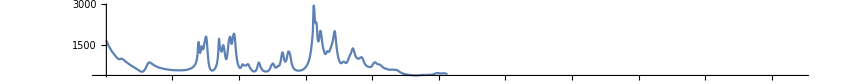

```mathematica
Plot[fittedFunction[x],{x,1,513},PlotRange->{{1,maxFreqN},All},Ticks->{ticksShifted,Automatic},AspectRatio->1/10]
```

```mathematica
Max[MultiplexerAverageSubA]*0.15
```

336.712

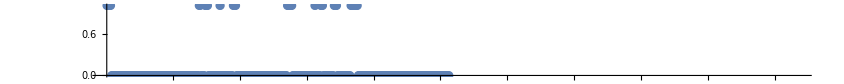

```mathematica
ListPlot[MaxDetect[MultiplexerAverageSubB,Max[MultiplexerAverageSubA]*0.15],PlotRange->{{1,maxFreqN},All},Ticks->{ticksShifted,Automatic},AspectRatio->1/10]
```